### Problem 4

```mathematica
q:=6
ϵ:=1
k:=1
```

```mathematica
(* Part C *)
```

Show that the coordinates of critical point

Tc = q e/2k
ρc =1/2
Pc =q e /2 (Ln2 − 1/2)
µc = −q.0fe

Feel free to use Mathematica to solve the necessary simultaneous equations.

In order to find Tc, Pc, ρc, and µc, we must find the point where dP/dV == d2P/dV2 == 0 (i.e. the slope and curvature are both flat). To do so, I define two functions, dP/dV and d2P/dV2 (less finicky than using Mathematica’s built-in derivative functions), and simultaneously solve them. The result will give us the values we are looking for.

I framed these equations in terms of N and V, rather than ρ, because ρ is easily recoverable from the other two and we have more control by separating the two variables from one another. Since we only have ρ and V, though, I had to define N using the ρ system established earlier on.

```mathematica
ρ0:=0.1

n[T_, V_]:=V*FindRoot[-6== T Log[ρ/(1-ρ)]-12 ρ, {ρ, ρ0}][[1,2]]
ρ[T_]:=FindRoot[-6== T Log[ρ/(1-ρ)]-12 ρ, {ρ, 0.1}][[1,2]]
P[T_, V_]:= T Log[1/(1-n[T, V]/V)]-6 (n[T,V]/V)^2
```

```mathematica
dPdV[T_, V_]:=(n[T, V]*k T)/(n[T, V]*(n[T, V]-V))-(2 (n[T, V])^2 q ϵ)/V^3
d2PdV2[T_, V_]:=-k T * ((n[T, V])^2/(V^4*(1-n[T, V]/V)^2)+2 n[T, V]/(V^2*(1-n[T, V]/V)))-(6 (n[T, V])^2 q ϵ)/V^4
```

```mathematica
Solve[{dPdV[T, V]==0, d2PdV2[T, V]==0}, {T, V}]
```

Since the Solve function didn’t seem to work, I tried plotting the two over one another and seeing visually where they zeroed out. Unfortunately, it looks like the same problem showed itself, and consequently it didn’t work out.

```mathematica
volume:=1
tMax:=10
Plot[{P[T],D[P[T], T]}, {T, 0,tMax}]

Plot[{P[T],dPdV[T, volume], d2PdV2[T, 11]}, {T, 0,tMax}]
Plot[{P[T],dPdV[T, volume], d2PdV2[T, 11]}, {T, 0,tMax}]
```

```mathematica
(* Part D *)
```

In this part, we wish to plot the coexistence densities as a function of temperature (the T−ρ phase diagram). 

However, like the Ising model, the transcendental equation µ(ρ,T) = µc cannot be analytically solved for ρ.

Thus, just as you did on homework 11 use the FindRoot function in Mathematica to solve the transcendental equation and thereby determine the value of ρ(T) at µc.

To find the liquid (high density), start your search with ρ>0.5,and vice-versa for the gas.To avoid the unstable solution at ρ=0.5, start far from 0.5.Using your function, plot ρ(T) at coexistence this is the ρ T phase diagram. Keep in mind there is no coexistence for T>Tc.

```mathematica
q:=6
ϵ:=1
k:=1
```

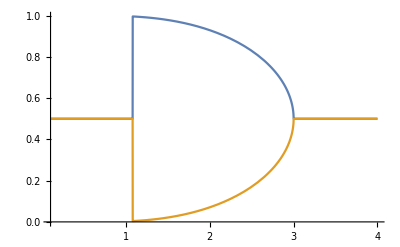

```mathematica
Plot[{FindRoot[-6== T Log[ρ/(1-ρ)]-12 ρ, {ρ, 0.9}][[1,2]],FindRoot[-6== T Log[ρ/(1-ρ)]-12 ρ, {ρ, 0.1}][[1,2]]}, {T, 0.1, 4}]
```

```mathematica
(* Part 4E *)
```

Now use the function you just wrote for ρ(T) and plug it in as an argument to P(ρ,T) in order to plot P(T) at coexistence (vapor pressure).

This is the P–T phase diagram, which should look quite familiar.

```mathematica
ρ[T_]:=FindRoot[-6== T Log[ρ/(1-ρ)]-12 ρ, {ρ, 0.1}][[1,2]]
P[T_]:= T Log[1/(1-ρ[T])]-6 (ρ[T])^2 ρ[2]
P[2]
```

0.0707202

-0.27763

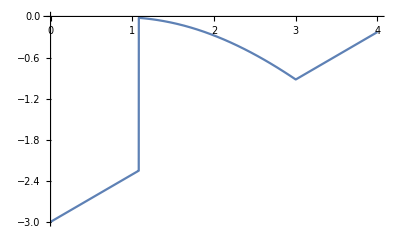

```mathematica
Plot[P[T], {T, 0, 4}]
```

Ultimately, most of these plots obviously didn’t work out, but I hope/think that was more a matter of Mathematica syntax than of understanding. But I guess I don’t know what I don’t know.

```mathematica
(* Problem 2 *)
ContourPlot3D[x+y+z==1,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-